```mathematica
sol[a_,b_]= {x[t],y[t]}/.DSolve[{ 
               x'[t]== 3x[t] - y[t],
	      y'[t]==x[t] + y[t],
               x[0] == a , 
               y[0]==b
                    },
                       {x[t],y[t]},
	       t
                        ];         (* utilizzo uguale, math può valutarla subito,
                  miglioro usando [a_,b_] =    *)
```

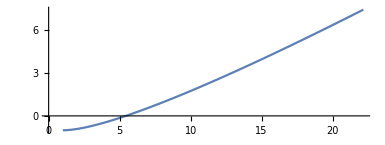

```mathematica
ParametricPlot[sol[1,-1],{t,0,1}]
```

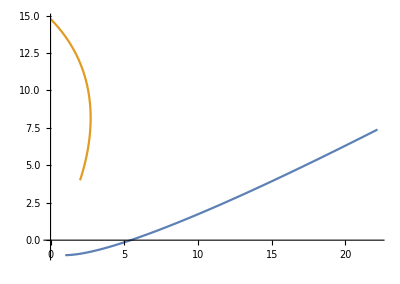

```mathematica
ParametricPlot[{sol[1,-1], sol[2,4]},{t,0,1}]
```

```mathematica
??Manipulate
```

Manipulate[expr,{u,u_min,u_max}] generates a version of expr with controls added to allow interactive manipulation of the value of u. 
Manipulate[expr,{u,u_min,u_max,du}] allows the value of u to vary between u_min and u_max in steps du. 
Manipulate[expr,{{u,u_init},u_min,u_max,…}] takes the initial value of u to be u_init. 
Manipulate[expr,{{u,u_init,u_lbl},…}] labels the controls for u with u_lbl. 
Manipulate[expr,{u,{u_1,u_2,…}}] allows u to take on discrete values u_1,u_2,…. 
Manipulate[expr,{u,…},{v,…},…] provides controls to manipulate each of the u,v,…. 
Manipulate[expr,c_u→{u,…},c_v→{v,…},…] links the controls to the specified controllers on an external device.

Attributes[Manipulate]={HoldAll,Protected,ReadProtected}
 
Options[Manipulate]={Alignment→Automatic,AppearanceElements→Automatic,AutoAction→False,AutorunSequencing→Automatic,BaselinePosition→Automatic,BaseStyle→{},Bookmarks→{},ContentSize→Automatic,ContinuousAction→Automatic,ControlAlignment→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,ControlPlacement→Automatic,ControlType→Automatic,DefaultBaseStyle→Manipulate,DefaultLabelStyle→ManipulateLabel,Deinitialization:>None,Deployed→False,Evaluator→Automatic,Frame→False,FrameLabel→None,FrameMargins→Automatic,ImageMargins→0,Initialization:>None,InterpolationOrder→Automatic,LabelStyle→{},LocalizeVariables→True,Method→{},Paneled→True,PreserveImageOptions→True,RotateLabel→False,SaveDefinitions→False,ShrinkingDelay→0,SynchronousInitialization→True,SynchronousUpdating→Automatic,TouchscreenAutoZoom→False,TouchscreenControlPlacement→Automatic,TrackedSymbols→Full,UndoTrackedVariables:>None,UnsavedVariables:>None,UntrackedVariables:>None}

```mathematica
(*-----------------------------------------------------------------------*)
```

```mathematica
sol2= DSolve[{
		     x'[t]== 2 x[t] -1,
		     y'[t]==(x[t]^2)-y[t]
		   },
		      {x[t],y[t]},
			t
                       ][[1]];     (* ho bisogno di scendere di un livello per poi effettuare il Dot (prodotto scalare tra due liste/vettori quando calcolo l'integrale) *)

gamma={x[t],y[t]}/.sol2;

gammapunto[t_]= D[gamma, t];

campo[t_]={    y[t]-x[t]^2    ,     2 x[t] -1     } /. sol2;


integral= Integrate[ campo[w].gammapunto[w] , {w,0,1}]
```

0

```mathematica
(*integrale nullo, il campo e la curva su cui sto integrando sono ortogonali *)
```

```mathematica
(*-----------------------------------------------------------------------*)
```

```mathematica
base[vect_List]:= Table[      
     u[j]= vect[[j]]- Sum[ ((vect[[j]].u[k-1])/(u[k-1].u[k-1])) u[k-1] , {k, 2, j}];
     u[j]= u[j]/(Sqrt[u[j].u[j]]);
     u[j],
              {j,1,Length[vect]}  
                                               ];
```

```mathematica
testList={{1,1},{1,2}}
```

{{1,1},{1,2}}

```mathematica
base[testList]
```

{{1/(√2),1/(√2)},{(1-(1/(√2)+√2)/(√2))/(√((1-(1/(√2)+√2)/(√2))^2+(2-(1/(√2)+√2)/(√2))^2)),(2-(1/(√2)+√2)/(√2))/(√((1-(1/(√2)+√2)/(√2))^2+(2-(1/(√2)+√2)/(√2))^2))}}

```mathematica
(*------------------------------------------------*)
```